```mathematica
eps0=8.85418781762039*10^-12;
k=1/eps0/4/Pi;
aw=3.03731419*10^6;
cw=1.14352594*10^6;
kappa=-3.84037247*10^10;
r0=0.0016622715189364113;
zw=3.80913378*10^(-1)*r0;
qw=9.64691720*10^-15;
qtop=-3.105494829523742*10^-15;
qbot=-2.589789085330693*10^-15;
(*dz= 0.0031863724551996647-0.0027886618943559704;*)
rp=4.445*10^-6;
rho=1500;
m=4.0/3.0*Pi*rp^3*rho;
trap=-1035598;
gamma= 4.341689383904344*m;
eqRtop=0.00034015213;
eqRbot=0.00012685477;
eqOmega=60;
eqPhi =  1.471;
```

```mathematica
ebotRad = {1, 0,0};
ebotTau = {0, 1,0};
etopRad = {Cos[dPhi], Sin[dPhi],0};
etopTau = {-Sin[dPhi], Cos[dPhi], 0};
```

```mathematica
rbotVec = {rbot, 0,0.0027886618943559704};
rtopVec = {rtop * Cos[dPhi], rtop*Sin[dPhi], 0.0031863724551996647 };
```

```mathematica
dist = Norm[rtopVec-rbotVec]; 
fbt =k * qtop * qbot/ dist^3*(rtopVec-rbotVec);

(*approved*)
dist  /. {rbot->eqRbot, rtop->eqRtop, dPhi->eqPhi}
```

0.000530444

```mathematica
fbtRad = Dot[fbt, etopRad];
fbtTau = Dot[fbt, etopTau];
```

```mathematica
coeff = Exp[-aw*(Sqrt[(rbotVec[[1]]-rtopVec[[1]])^2 + (rbotVec[[2]]-rtopVec[[2]])^2])^2-cw*(-rbotVec[[3]]+rtopVec[[3]]-zw)^2];

ftbWake =qbot *coeff*k*qw/r0 *
{2*aw*(rbotVec[[1]]-rtopVec[[1]]),
2*aw*(rbotVec[[2]]-rtopVec[[2]]),
 2*cw*(-rbotVec[[3]]+rtopVec[[3]] - zw)};
(**)
ftbWake /. {rtop->eqRtop, rbot->eqRbot, dPhi->eqPhi}

(*approved*)
Norm[ ftbWake / qbot /. {rbot->eqRbot, rtop->eqRtop, dPhi->eqPhi}]
(*approved*)
Norm[ fbt/qtop /. {rbot->eqRbot, rtop->eqRtop, dPhi->eqPhi}]
```

{-6.89676×10^-15,2.51091×10^-14,6.57686×10^-14}

27.3133

82.723

```mathematica
ftb[kWake_] := -fbt +kWake* ftbWake;
ftb[1.0]/. {rtop->eqRtop, rbot->eqRbot, dPhi->0.05}
ftb[0.95]/. {rtop->eqRtop, rbot->eqRbot, dPhi->0.05}
fbt /. {rtop->eqRtop, rbot->eqRbot, dPhi->0.05}
```

SetDelayed::write: Tag List in «1»[kWake_] is Protected.

{-1.51103×10^-13,-1.20674×10^-14,-2.45177×10^-13}[1.]

{-1.51103×10^-13,-1.20674×10^-14,-2.45177×10^-13}[0.95]

{1.67272×10^-13,1.33587×10^-14,3.12514×10^-13}

```mathematica
ftbRad[kWake_] := Dot[ftb[kWake], ebotRad];
ftbTau[kWake_] := Dot[ftb[kWake], ebotTau];
```

SetDelayed::write: Tag Plus in (-8.20563×10^-11 ⅇ^(-0.0634046-303731. (Abs[«1»]^2+Abs[«1»]^2)) (rbot-rtop Cos[dPhi])-(«1»)/(«1»)^(3/2)+(1.88219×10^-30 ⅇ^(«24» √(«23»+«1»+«1»)) (-rbot+rtop Cos[dPhi]))/(1.58174×10^-7+Abs[Times[«2»]+«1»]^2+Abs[rtop Sin[«1»]]^2))[kWake_] is Protected.

SetDelayed::write: Tag Plus in (8.20563×10^-11 ⅇ^(-0.0634046-303731. (Abs[«1»]^2+Abs[«1»]^2)) rtop Sin[dPhi]-(7.22831×10^-20 «2» Sin[dPhi])/((«23»+«1»+(«1»)^2)^(3/2))+(1.88219×10^-30 ⅇ^(2.60391×10^-11 «1») rtop Sin[dPhi])/(1.58174×10^-7+Abs[«1»]^2+Abs[rtop Sin[«1»]]^2))[kWake_] is Protected.

```mathematica
eqns[kWake_] := {
fbtTau/rtop-ftbTau[kWake]/rbot==0, 
1/2/gamma*(fbtTau/rtop+ftbTau[kWake]/rbot)==Omega, 
rtop*(qtop*trap-m*Omega^2)==fbtRad, 
rbot*(qbot*trap-m*Omega^2)==ftbRad[kWake]
};
initgss={{rtop, eqRtop}, {rbot,eqRbot}, {Omega,eqOmega},{dPhi,eqPhi}};
```

SetDelayed::write: Tag List in {-(8.20563×10^-11 ⅇ^Plus[«2»] rtop Sin[dPhi]-(«23» «2» Sin[dPhi])/(«1»)^(3/2)+(1.88219×10^-30 «1» «4» Sin[dPhi])/Plus[«3»])/rbot+(-((Times[«4»]+Times[«4»]) Sin[dPhi])+Cos[dPhi] (Times[«5»]+Times[«1»]))/rtop==0,«23» («1»+«1»)==«5»,«1»,(2.68198×10^-9-5.51817×10^-13 Omega^2) rbot==«1»}«1»«6»] is Protected.

```mathematica
sol=FindRoot[eqns[1.0],initgss, MaxIterations->1000]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

{rtop→0.000150082,rbot→0.00119829,Omega→60.,dPhi→1.471}

```mathematica
expr1 =ftbRad[1.0] /. {rtop->eqRtop, rbot->eqRbot, dPhi->eqPhi};
expr2 =fbtRad /. {rtop->eqRtop, rbot->eqRbot, dPhi->eqPhi};

expr1 < 0
expr2 > 0
```

False

True

1.91861×10^-13

2.56896×10^-13

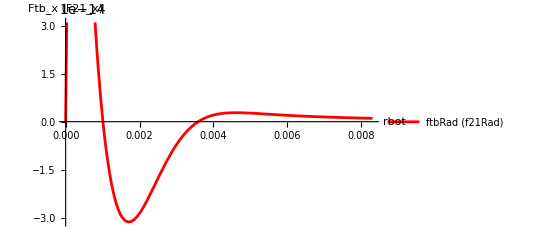

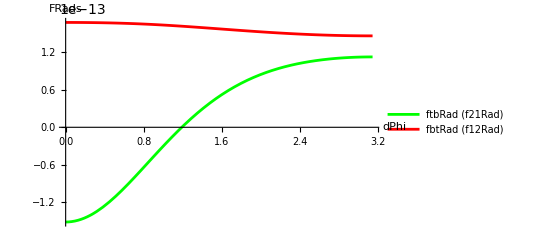

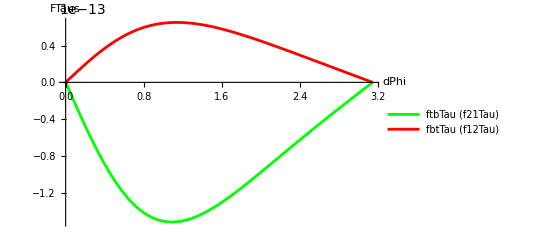

```mathematica
Norm[ftb[1.0] /. {rtop->eqRtop, rbot->eqRbot, dPhi->eqPhi}]
Norm[fbt /. {rtop->eqRtop, rbot->eqRbot, dPhi->eqPhi}]

(*Plot[{Norm[ftb[1.0] /. {rtop->eqRtop, rbot->eqRbot}], Norm[fbt /. {rtop->eqRtop, rbot->eqRbot}]}, {dPhi, 0, Pi}, AxesLabel->{"dPhi", "Mods"}, PlotLegends->{"Mod(ftb) (f21)", "Mod(fbt) (f12)"}, PlotStyle->{Green, Red}]

Plot[{Norm[ftb[10.0] /. {rtop->eqRtop, rbot->eqRbot}], Norm[fbt /. {rtop->eqRtop, rbot->eqRbot}]}, {dPhi, 0, Pi}, AxesLabel->{"dPhi", "Mods"}, PlotLegends->{"Mod(ftb) (f21)", "Mod(fbt) (f12)"}, PlotStyle->{Green, Red}]

Plot[{Norm[ftb[0.1] /. {rtop->eqRtop, rbot->eqRbot}], Norm[fbt /. {rtop->eqRtop, rbot->eqRbot}]}, {dPhi, 0, Pi}, AxesLabel->{"dPhi", "Mods"}, PlotLegends->{"Mod(ftb) (f21)", "Mod(fbt) (f12)"}, PlotStyle->{Green, Red}]*)

(**)

Plot[{ftb[1.0][[1]] /. {rtop->0,  dPhi->0}}, {rbot, 0, r0*5}, AxesLabel->{"rbot", "Ftb_x (F21_x)"}, PlotLegends->{"ftbRad (f21Rad)", "fbtRad (f12Rad)"}, PlotStyle->{Green, Red}]

Plot[{ftbRad[1.0] /. {rtop->eqRtop, rbot->eqRbot}, fbtRad /. {rtop->eqRtop, rbot->eqRbot}}, {dPhi, 0, Pi}, AxesLabel->{"dPhi", "FRads"}, PlotLegends->{"ftbRad (f21Rad)", "fbtRad (f12Rad)"}, PlotStyle->{Green, Red}]

Plot[{ftbTau[1.0] /. {rtop->eqRtop, rbot->eqRbot}, fbtTau /. {rtop->eqRtop, rbot->eqRbot}}, {dPhi, 0, Pi}, AxesLabel->{"dPhi", "FTaus"},  PlotLegends->{"ftbTau (f21Tau)", "fbtTau (f12Tau)"}, PlotStyle->{Green, Red}]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {rtop,rbot,Omega,dPhi} = {0.000494244,0.000241618,60.,1.471}. Try perturbing the initial point(s).

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::jsing: Encountered a singular Jacobian at the point {rtop,rbot,Omega,dPhi} = {0.00015039,0.00186587,60.,1.471}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {rtop,rbot,Omega,dPhi} = {0.0000840935,0.00207865,60.,1.471}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

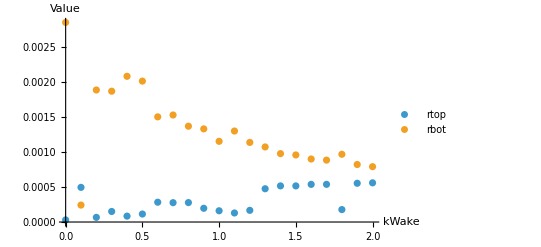

```mathematica
kWakeValues=Range[0,2.0,0.1];
solutions=Table[sol=FindRoot[eqns[kWake], initgss];
{kWake,rtop/. sol,rbot/. sol,Omega/. sol,dPhi/. sol},{kWake,kWakeValues}];

ListPlot[{solutions[[All,{1,2}]],solutions[[All,{1,3}]]},PlotLegends->{"rtop","rbot"},AxesLabel->{"kWake","Value"},PlotRange->All]
```

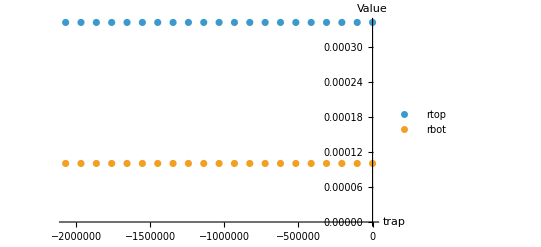

```mathematica
trapValues=trap*Range[0.0,2.0,0.1]; 
solutions=Table[trap=trapVal;
sol=FindRoot[eqns[1.0],initgss];
{trapVal,rtop/. sol,rbot/. sol,Omega/. sol,dPhi/. sol},{trapVal,trapValues}];
ListPlot[{solutions[[All,{1,2}]],solutions[[All,{1,3}]]},PlotLegends->{"rtop","rbot"},AxesLabel->{"trap","Value"},PlotRange->All]
```